```mathematica
F[x_]=3 x^4-16 x^3+24x; (*задана функція*)
```

```mathematica
A=3.; (*початок відрізку пошуку*) 
B=4.; (*кінець відрізку пошуку*)

ϵ=0.001;      (*точність*)
```

```mathematica
result={};
```

```mathematica
min=Minimize[F[x], A<x<B, x] (*знаходження мінімума функції*)
```

{-161.568,{x→3.8662}}

```mathematica
(*Графік функції*)
```

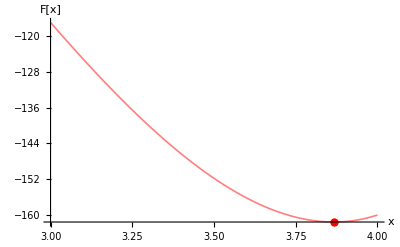

```mathematica
Plot[F[x], {x, A, B}, PlotRange->All, PlotStyle-> {Pink,Thickness[0.003]}, AxesLabel->{x, "F[x]"}, Epilog->{Red, PointSize[0.015], Point[{min[[2,1,2]], min[[1]] }]}]
```

```mathematica
(*Метод дихотомії*)
```

```mathematica
a=A;
b=B;
AB={};
AppendTo[AB,{a,b}];
t11=AbsoluteTime[]; (*початок часу роботи методу*)
(*1 ітерація*)
k=0;
x0=(a+b)/2; (*середина відрізку*)
Fx0=F[x0];
x1k=x0-ϵ/2;  (*ліворуч*)
x2k=x0+ϵ/2;  (*праворуч*)
Fx={F[x1k], F[x2k]}; (*значення фу-ції в x1k,x2k*)
res1={};
AppendTo[res1,{0,x1k,x2k,Fx[[1]],Fx[[2]], Abs[b-a]}];
(*вибіраємо новий відрізок*)
If[Fx[[1]]< Fx[[2]], {a=a, b=x0}, {a=x0, b=b}];
AppendTo[AB,{a,b}];
(*цикл методу*)
For[k = 1, k < 100000, k++ ,
{x0=(AB[[-1,1]]+AB[[-1,2]])/2;
Fx0=F[x0];
x1k=x0-ϵ/2; 
x2k=x0+ϵ/2;
 Fx={F[x1k], F[x2k]};
If[Fx[[1]]< Fx[[2]], {a=a, b=x0, AppendTo[AB,{a,b}]}, {a=x0, b=b, AppendTo[AB,{a,b}]}];
AppendTo[res1,{k,x1k,x2k,Fx[[1]],Fx[[2]],N[Abs[AB[[-1,2]]-AB[[-1,1]]]]}];
If[Abs[AB[[-1,2]]-AB[[-1,1]]]≤  ϵ,  Break[]];(*умова виходу з цикла*)
If[k > 100, Break[]] (*щоб не потрапити у нескінечний цикл*)}] 
t22=AbsoluteTime[]; (*кінець часу роботи метода*)
(*заповнення таблиці*)
Grid[Prepend[res1,{"k","x_k-ϵ/2","x_k+ϵ/2","F[x1k]"," F[x2k]","Abs[b-a]"}]]
Print["Час роботи циклу\t",t=t22-t11,"\nОтримане наближення\t", N[xs=(a+b)/2],"\nЗначення функції\t",N[ F[xs]],"\nДовжина інтервалу невизначеності\t",N[ Abs[b-a]]]
c=min[[2,1,2]];
A1=Abs[xs-c]
AppendTo[result,{k+1,a,b,Abs[b-a],A1,t,2(k+1),xs,F[xs]}];
```

k | x_k-ϵ/2 | x_k+ϵ/2 | F[x1k] |  F[x2k] | Abs[b-a]
0 | 3.4995 | 3.5005 | -151.788 | -151.837 | 1.
1 | 3.7495 | 3.7505 | -160.479 | -160.497 | 0.25
2 | 3.8745 | 3.8755 | -161.562 | -161.561 | 0.125
3 | 3.812 | 3.813 | -161.328 | -161.337 | 0.0625
4 | 3.84325 | 3.84425 | -161.525 | -161.528 | 0.03125
5 | 3.85888 | 3.85988 | -161.564 | -161.565 | 0.015625
6 | 3.86669 | 3.86769 | -161.568 | -161.568 | 0.0078125
7 | 3.86278 | 3.86378 | -161.567 | -161.568 | 0.00390625
8 | 3.86473 | 3.86573 | -161.568 | -161.568 | 0.00195313
9 | 3.86571 | 3.86671 | -161.568 | -161.568 | 0.000976563

Час роботи циклу	0.0060266
Отримане наближення	3.86572
Значення функції	-161.568
Довжина інтервалу невизначеності	0.000976563

0.000475606